# Figure 1 (PDF)

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

#### M=5 (with MC simulation)

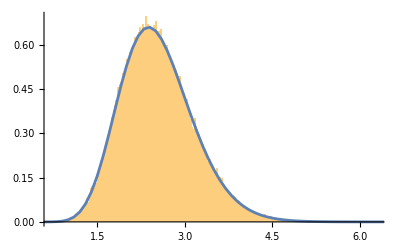

```mathematica
ClearAll["Global`*"];
M=5;
Subscript[mv, 1]={10/10,12/10};Subscript[mv, 2]={14/10,16/10};Subscript[mv, 3]={18/10,20/10};Subscript[mv, 4]={22/10,24/10};Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};Subscript[mv, 7]={34/10,36/10};Subscript[mv, 8]={38/10,40/10};Subscript[mv, 9]={42/10,44/10};Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};Subscript[ov, 2]={24/10,26/10};Subscript[ov, 3]={28/10,30/10};Subscript[ov, 4]={32/10,34/10};Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};Subscript[ov, 7]={44/10,46/10};Subscript[ov, 8]={48/10,50/10};Subscript[ov, 9]={52/10,54/10};Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
R1=∑_(j=1)^M ER[j,1];
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;UB=20;Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T1=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T,Joined->True,PlotTheme->"Detailed",PlotRange->All]]
Δs=2;γdbs=Table[10^(i/20),{i,LB,UB,Δs}];γss=Table[i,{i,LB,UB,Δs}];
T1S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

#### M=6

```mathematica
M=6;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
R1=∑_(j=1)^M ER[j,1];
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;
UB=20;
Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T2=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T,Joined->True,PlotTheme->"Detailed",PlotRange->All]];
Δs=2;
γdbs=Table[10^(i/20),{i,LB,UB,Δs}];
γss=Table[i,{i,LB,UB,Δs}];
T2S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

#### M=7

```mathematica
M=7;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
R1=∑_(j=1)^M ER[j,1];
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;
UB=20;
Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T3=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T,Joined->True,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All]];
Δs=2;
γdbs=Table[10^(i/20),{i,LB,UB,Δs}];
γss=Table[i,{i,LB,UB,Δs}];
T3S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

#### M=8

```mathematica
M=8;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
R1=∑_(j=1)^M ER[j,1];
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;
UB=20;
Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T4=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T1,Joined->True,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All]];
Δs=2;
γdbs=Table[10^(i/20),{i,LB,UB,Δs}];
γss=Table[i,{i,LB,UB,Δs}];
T4S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

#### M=9

```mathematica
M=9;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;
UB=20;
Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T5=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T1,Joined->True,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All]];
Δs=2;
γdbs=Table[10^(i/20),{i,LB,UB,Δs}];
γss=Table[i,{i,LB,UB,Δs}];
T5S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

#### M=10

```mathematica
M=10;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};

ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/(M Gamma[Sol[[1,2]]+1/Sol[[2,2]]]));
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
T=Table[{r,(α1 μ1^μ1 r^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 r^α1)/Ω1^α1]},{r,1/1000,40,1/10}];
LB=-10;
UB=20;
Δ=1/2;
γdb=Table[10^(i/20),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T6=Table[{γs[[i]],(α1 μ1^μ1 γdb[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdb[[i]]^α1)/Ω1^α1]},{i,1,Length[γdb]}];
sample=10^5;
H=(∑_(i=1)^M ∏_(j=1)^2 RandomVariate[ NakagamiDistribution[Subscript[mv, i][[j]],Subscript[ov, i][[j]]],sample])/M;
Histogram[H,200,"PDF",PlotRange->All,Epilog->First@ListPlot[T1,Joined->True,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All]];
Δs=2;
γdbs=Table[10^(i/20),{i,LB,UB,Δs}];
γss=Table[i,{i,LB,UB,Δs}];
T6S=Table[{γss[[i]],(α1 μ1^μ1 γdbs[[i]]^(α1 μ1-1))/(Ω1^(α1 μ1)Gamma[μ1])Exp[(-μ1 γdbs[[i]]^α1)/Ω1^α1]},{i,1,Length[γdbs]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

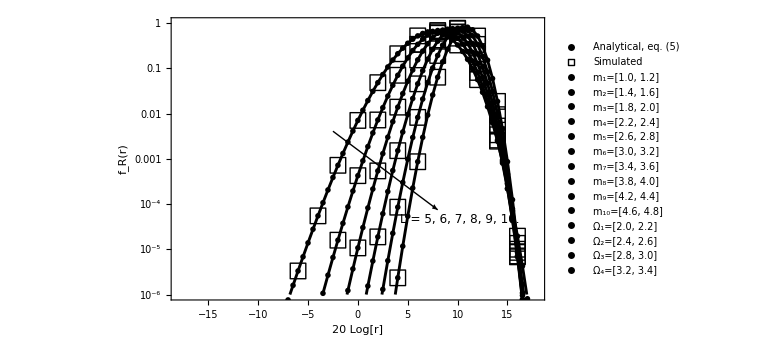

```mathematica
F1=ListLogPlot[{T1,T2,T3,T4,T5,T6,T1S,T2S,T3S,T4S,T5S,T6S},PlotStyle->{{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},Black,Black,Black,Black,Black,Black},Joined->{True,True,True,True,True,True,False,False,False,False,False,False},PlotMarkers->{{"",16},{"",16},{"",16},{"",16},{"",16},{"",16},{"□",16},{"□",16},{"□",16},{"□",16},{"□",16},{"□",16}},GridLines->Automatic,GridLinesStyle->Directive[White,Dashed,Thin],Frame-> True,FrameStyle->Directive[Black,18,FontFamily-> "Helvetica"],FrameLabel->{"20 Log[r]","f_R(r)"},ImageSize->Large,PlotRange->{{-18,18},{10^-6,1}},Axes->False,Epilog->{Text[Style["L = 5, 6, 7, 8, 9, 10.",12],{10.2,-10}],{Arrowheads[Medium],Black,Arrow[{{-2.5,-5.5},{8,-9.5}}]}},PlotLegends->{Placed[LineLegend[{Black,Black},{"Analytical, eq. (5)","Simulated"},Joined->{False,False},LegendMarkers->{{"-",16},{"□",16}},LabelStyle->{Black,14,FontFamily-> "Helvetica"}],{0.2,0.9}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"m_1=[1.0, 1.2]","m_2=[1.4, 1.6]","m_3=[1.8, 2.0]","m_4=[2.2, 2.4]","m_5=[2.6, 2.8]","m_6=[3.0, 3.2]","m_7=[3.4, 3.6]","m_8=[3.8, 4.0]","m_9=[4.2, 4.4]","m_10=[4.6, 4.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,9,FontFamily-> "Helvetica"}],{0.06,0.40}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"Ω_1=[2.0, 2.2]","Ω_2=[2.4, 2.6]","Ω_3=[2.8, 3.0]","Ω_4=[3.2, 3.4]","Ω_5=[3.6, 3.8]","Ω_6=[4.0, 4.2]","Ω_7=[4.4, 4.6]","Ω_8=[4.8, 5.0]","Ω_9=[5.2, 5.4]","Ω_10=[5.6, 5.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,9,FontFamily-> "Helvetica"}],{0.19,0.40}]},FrameTicks->{{{{1,"1"},{0.1,"10^-1"},{0.01,"10^-2"},{10^-3,"10^-3"},{10^-4,"10^-4"},{10^-5,"10^-5"},{10^-6,"10^-6"}},None},{Automatic,None}}]
```